## Practica AFN - Epsilon

## Helper Functions

```mathematica
ShowGraphFA[edges_,states_List,q0_,q_List,edgelabels_]:=Graph[
edges,
VertexSize->0.55,
VertexLabels->Placed["Name",Center],
VertexStyle->Join[{0->White},Map[(#->Red)&,q]],
EdgeWeight->edgelabels,
EdgeLabels->"EdgeWeight"
]
```

```mathematica
FATable[δ_,states_,Σ_]:=Grid[
Join[List/@Prepend[states,"Q\Σ"],Prepend[Partition[Flatten[Outer[δ[{#1,#2}]/._Missing->"-"&,states,Σ,1],1],Length[Σ]],Σ],2],
Alignment->Center,
Spacings->{2,1},
Frame->All,
ItemStyle->"Text",
Background->{{Gray,None},{LightGray,None}}
]
```

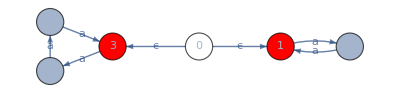

```mathematica
ShowGraphFA[{0->1,0->3,1->2,2->1,3->4,4->5,5->3},{0,1,2,3,4,5},{0},{1,3},{"ϵ","ϵ","a","a","a","a","a"}]
```

```mathematica
δ=Association[
{0,ϵ}->{1,3},
{1,"a"}->{2},
{2,"a"}->{1},
{3,"a"}->{4},
{4,"a"}->{5},
{5,"a"}->{3}
];
```

```mathematica
FATable[δ,{0,1,2,3,4,5},{ϵ,"a"}]
```

Q\Σ | ϵ | a
0 | {1,3} | -
1 | - | {2}
2 | - | {1}
3 | - | {4}
4 | - | {5}
5 | - | {3}

Primero toca obtener los estados a los que va cada “key”, ejemplo {0, ϵ}

```mathematica
Table[δ[{#1[[i]],ϵ}]/._Missing->{},{i,Length[#1]}]&[{0}]
```

{{1,3}}

```mathematica
Table[δ[{#1[[i]],"a"}]/._Missing->{},{i,Length[#1]}]&[{1}]
```

{{2}}

Ahora toca hacer la union, lo podemos hacer de esta manera

```mathematica
NestWhileList[Union@@Table[δ[{#1[[i]],ϵ}]/._Missing->{},{i,Length[#1]}]&,{0},#≠ {}&]
```

{{0},{1,3},{}}

Tenemos que eliminar los estados vacios

```mathematica
Most[NestWhileList[Union@@Table[δ[{#1[[i]],ϵ}]/._Missing->{},{i,Length[#1]}]&,{0},#≠ {}&]/._Missing->{}]
```

{{0},{1,3}}

Ahora debemos crear la Union de a donde van estos estados

```mathematica
Closure[δ_,state_List]:=Union[Map[Flatten[Most[NestWhileList[Union@@Table[δ[{#1[[i]],ϵ}]/._Missing->{},{i,Length[#1]}]&,{#},#≠ {}&]/._Missing->{}]]&,state]//Flatten]
```

```mathematica
Closure[δ,{0}]
```

{0,1,3}